# Double Pendulum

## The Bashforth-Adam Approximation

## Defining the function

The Euler approximation was used to generate the inital conditions.

```mathematica
tt=0; δt=0.001;niter=10000;k=10;
thetaPast = 1; uPast = 1;
θ=thetaPast +δt uPast;
u =uPast -δt k^2 Sin[thetaPast];

rr=Reap[
Do[
(* Update θ here *)
utemp=u;

u+=-(k^2 δt Sin[θ])(3/2) + (1/2)(δt k^2 Sin[thetaPast]);
θ+=δt utemp + (3/2)(δt utemp)-(3/2)(δt uPast);

tt+= δt; (* Update t *)
thetaPast = θ;
uPast = u;
Sow[{tt,θ}]; (* Output *)

,{i,niter}]
];
```

#### Checking the Error

The variables θ, k, and δt are globally defined to see how changing them effects the error.

Bashforth-Adams approximation.

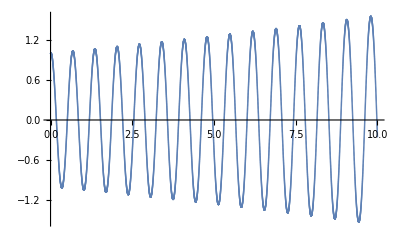

```mathematica
ListPlot[rr⟦2,1⟧]
```

Analytical solution:

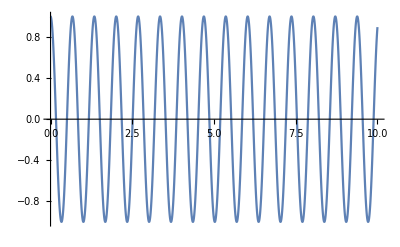

```mathematica
Actual[t_]=2 ArcSin[Sin[θ0/2] JacobiSN[EllipticK[Sin[θ0/2]^2]-k1 t,Sin[θ0/2]^2]]/.{θ0->1, k1->10};
(* Here's the analytical solution-- we took it from the Notebook Atherton left us. We plotted it, just to make sure it resembled our approximation. *)

Plot[2 ArcSin[JacobiCD[10 t,Sin[1/2]^2] Sin[1/2]], {t, 0, 10}]
```

Error plot

```mathematica
thetaAn = 0; error = 0;
rError=Reap[
Do[
utemp=u;

u+=-(k^2 δt Sin[θ])(3/2) + (1/2)(δt k^2 Sin[pTheta]);
θ+=δt utemp + (3/2)(δt utemp)-(3/2)(δt upast);
thetaAn = 2 ArcSin[JacobiCD[10 (tt),Sin[1/2]^2] Sin[1/2]];
error = (thetaAn - Actual[θ]);

tt+= δt; 
pTheta = θ;
upast = u;
Sow[{tt,error}]; 

,{i,niter}]
];

ListPlot[rError⟦2, 1⟧]
```

Part::partw: Part 1 of {} does not exist.

ListPlot::lpn: {Null, {}} ⟦ 2, 1 ⟧ is not a list of numbers or pairs of numbers.

ListPlot[{Null,{}}⟦2,1⟧]

#### Plotting the pendulum

Get angles from the function

```mathematica
lOne = 1; lTwo = 1;
t1 = Table[rr[[ 2, 1, i, 2]],{i, niter}];
t2 = Table[rr[[ 2, 1, i, 3]],{i, niter}];
```

Get x,y coordinates based on the angles

```mathematica
x1=Table[{lOne Sin[t1[[i]]],-lOne Cos[t1[[i]]]}, {i, niter}];
x2=Table[{x1[[ i, 1]] + lTwo  Sin[t2[[i]]],x1[[i, 2]] -lTwo Cos[t2[[i]]]}, {i, niter}];

marker1=Graphics[{Blue,Disk[]}];
marker2=Graphics[{Red,Disk[]}];
p1 = ListPlot[x1,PlotMarkers->{marker1, .03}, PlotRange->{{-1,1},{-1,1}}];
p2 = ListPlot[x2, PlotMarkers-> {marker2, .03}];
Show[p1, p2, PlotRange -> {{-2, 2},{-2, 2}}]
```

Animation function: notice how it speeds up as time increases, this is due to the overestimation of the Bashford-Adams approximation.

```mathematica
Animate[
Graphics[{
Point[x1[[i]]],
Point[x2[[i]]], 
Line[{{0,0},x1[[i]]}],
Line[{x1[[i]],x2[[i]]}]},
  PlotRange->{{-2,2},{-2,2}}
],
{i, 1 , niter,1},
 AnimationRate->100
]
```